```mathematica
list = Import[NotebookDirectory[]<>"/res/out_1.5_2.0.txt","Table"];
Length[list]
len=Length[list[[1]]]
```

50

501

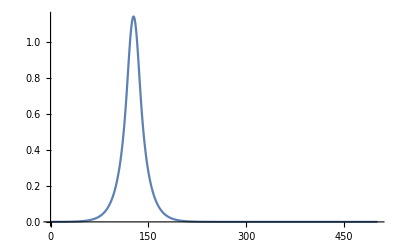

```mathematica
ListLinePlot[-list[[2]],PlotRange->All]
```

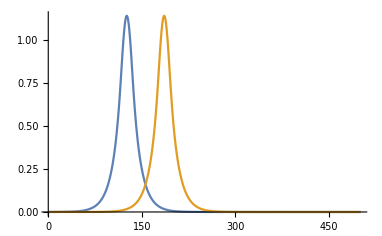

```mathematica
ListLinePlot[{-list[[1]],-list[[-1]]},PlotRange->Full]
```

```mathematica
f1=NIntegrate[Interpolation[list[[1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[list[[-1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
(f2-f1)/f1
```

27.1576

27.1581

0.0000190716